```mathematica
ClearAll[tex,tf,mf,df,primeQpos,tr,u,id, bnTab];
SetAttributes[tex,HoldFirst]
tex[exp_]:=TeXForm[HoldForm[exp]]
tf:=TableForm
mf:=MatrixForm
df:=Defer
primeQpos[n_]:=If[PrimeQ[n]&&n>0,True,False]
tr:=Trace
u[m_Integer]:=1
id[m_Integer]:=Floor[1/m]
bnTab[j_]:=Table[Binomial[n,k],{n,0,j},{k,0,n}]
```

https://math.stackexchange.com/questions/136417/what-is-so-interesting-about-the-zeroes-of-the-riemann-zeta-function/136488#136488

## Topic

### Definition / Theorem

This is text.

#### Example

# Notes ANT

Numerical Methods and Tools

## Bernoulli Polynomials

### Definition / Theorem

#### Example

```mathematica
Manipulate[
Column[{Plot[BernoulliB[k,x],{x,0,1}],BernoulliB[k,x],BernoulliB[k]}],{k,1,6,1}]
```

## Euler-MacLaurin Summation

### Definition / Theorem

#### Example: First Order

```mathematica
ClearAll[f]
```

```mathematica
f[k_]:=k^4+2k
f[k_]:=1/(√k)
Sum[f[k],{k,1,100}]//N
```

18.5896

```mathematica
Integrate[f[x],{x,1,5}]-1/2(f[5]-f[1])//N;
g[n_]=Integrate[f[x],{x,1,n+1},Assumptions->{n>0}]-1/2(f[n+1]-f[1])//Expand//Simplify
g[100]//N
```

(3+4 n-3 √(1+n))/(2 √(1+n))

18.55

#### Example: Second Order

```mathematica
ClearAll[f]
```

```mathematica
f[k_]:=k^4+2k
f[k_]:=1/(√k+k^2)
Sum[f[k],{k,1,4}]//N
```

0.833433

```mathematica
Integrate[f[x],{x,1,5}]-1/2(f[5]-f[1])+1/12(f'[5]-f'[1])//N;
g[n_]=Integrate[f[x],{x,1,n+1},Assumptions->{n>0}]-1/2(f[n+1]-f[1])+1/12(f'[n+1]-f'[1])//Expand//Simplify
g[4]//N//Chop
```

1/288 (87-48/((√(1+n)+(1+n)^2)^2)-(48 n)/((√(1+n)+(1+n)^2)^2)-12/(√(1+n) (√(1+n)+(1+n)^2)^2)-144/(√(1+n)+(1+n)^2)+64 √3 π-64 Log[8]+192 Log[1+1/(√(1+n))]-192 (-1)^(1/3) Log[1-(-1)^(1/3)/(√(1+n))]+192 (-1)^(2/3) Log[1+(-1)^(2/3)/(√(1+n))])

0.836458

## Euler’s Summation Formula

### Definition

∑_(y<n⩽x) f(n) = ∫_y^x f(t)ⅆt +∫_y^x (t-[t])f'(t)ⅆt+ f(x)([x]-x)-f(y)([y]-y)

∑_(1<n⩽x) f(n) = ∫_1^x f(t)ⅆt +∫_1^x (t-[t])f'(t)ⅆt+ f(1)+f(x)([x]-x)

#### Example

## Abel Summation

### Definition

∑_(y<n⩽x) a(n) f(n) = A(x) f(x)-A(y)f(y)-∫_y^x A(t)f'(t)ⅆt

#### Example

Arithmetical Functions

## Harmonic Numbers

```mathematica
ClearAll[r,s,t,t1,t2,t3,t4]
r[n_]:=Binomial[(n+1)!+n,n]
s[n_]:=(r[n]-1)/((n+1)!)
t[n_]:=s[n]-(n+1)Floor[s[n]/(n+1)]
t1[n_]:=Mod[s[n],n+1]
t2[n_]:=Expand[Pochhammer[x+1,n]][[2]]/(x n!)
t3[n_]:=-StirlingS1[n+1,2]/StirlingS1[n+1,1]
t4[n_]:=Mod[Pochhammer[(n+1)!,n+1]/(n! ((n+1)!)^2)-1/((n+1)!),n+1]
```

```mathematica
1764/720
HarmonicNumber[6]
t[6]
t1[6]
t2[6]
t3[6]
t4[6]
```

49/20

49/20

49/20

«4 more identical outputs»

```mathematica
25 26 27
Pochhammer[25,3]
```

17550

17550

```mathematica
t4[n_]:=Mod[Pochhammer[(n+1)!,n+1]/(n! ((n+1)!)^2)-1/((n+1)!),n+1]
1+1/4+1/9
Expand[(x+1)(x+4)]
Expand[(x+2)(x+3)]
Expand[(x+1)(x+2)(x+3)(x+4)]
(24+50 x+35 x^2+10 x^3+x^4)/(6+5x+x^2)//Simplify
((x+1)(x+2)(x+3)(x+4)(x+1)(x+4))/((x+1)(x+2)(x+3)(x+4))//Simplify//Expand
```

49/36

4+5 x+x^2

6+5 x+x^2

24+50 x+35 x^2+10 x^3+x^4

4+5 x+x^2

4+5 x+x^2

```mathematica
Expand[(x+1)(x/2+1)(x/3+1)(x/4+1)(x/5+1)(x/6+1)]
```

1+(49 x)/20+(203 x^2)/90+(49 x^3)/48+(35 x^4)/144+(7 x^5)/240+x^6/720

```mathematica
HarmonicNumber[4,2]
(7/6)^2
```

205/144

49/36

```mathematica
tt1[n_]:=ⅇ^EulerGamma n Log[Log[n]]
tt1[10^8000]//N
```

1.74923205562703×10^8001

## Highest power of prime p in n!

```mathematica
ClearAll[f]
f[n_,p_]:=Sum[Floor[n/p^i],{i,1,Ceiling[N[Log[n]]/Log[p]]}]/;p≤n
```

```mathematica
f[10,2]
f[10,3]
f[10,5]
f[10,7]
```

8

4

2

1

```mathematica
10!
```

3628800

```mathematica
2^8 3^4 5^2 7
```

3628800

## Moebius Function

### Definition

The Moebius function is defined as follows:
if n > 1 write n as n = ∏_(i=1)^k (p^α_i)_i and
	μ(1) = 1;
	μ(n) = (-1)^k if α_i=1 for all i
	μ(n) = 0 otherwise.

#### Example

```mathematica
TableForm[Table[{k,MoebiusMu[k]},{k,Divisors[12]}],TableHeadings->{None,{"k","μ[k]"}},TableAlignments->{Right}]
```

k | μ[k]
1 | 1
2 | -1
3 | -1
4 | 0
6 | 1
12 | 0

```mathematica
TableForm[Table[{k,MoebiusMu[k]},{k,1,12}],TableHeadings->{None,{"k","μ[k]"}},TableAlignments->{Right}]
```

k | μ[k]
1 | 1
2 | -1
3 | -1
4 | 0
5 | -1
6 | 1
7 | -1
8 | 0
9 | 0
10 | 1
11 | -1
12 | 0

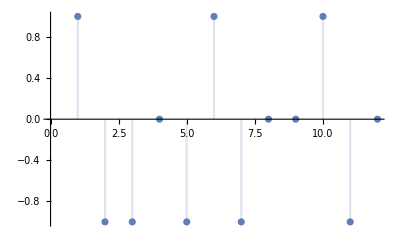

```mathematica
DiscretePlot[MoebiusMu[k],{k,12},AxesOrigin->{0,0}]
```

## Euler totient Function

### Definition

If n ≳ 1 the Euler totient ϕ(n) is defined to be the number of positive integers not exceeding n which are relatively prime to n.

Sum formula: n = ∑_(d/n) ϕ(d)

	n = ∑_(d/n) ϕ(d)
	ϕ(n) = ∑_(d/n) μ(n/d)d

Product formula: write n as n = ∏_(i=1)^k (p^α_i)_i and
	ϕ(n) = n∏_(i=1)^k (1-1/p_i)

#### Example

```mathematica
TableForm[Table[{k,EulerPhi[k]},{k,1,20}],TableHeadings->{None,{"k","ϕ[k]"}},TableAlignments->{Right}]
```

k | ϕ[k]
1 | 1
2 | 1
3 | 2
4 | 2
5 | 4
6 | 2
7 | 6
8 | 4
9 | 6
10 | 4
11 | 10
12 | 4
13 | 12
14 | 6
15 | 8
16 | 8
17 | 16
18 | 6
19 | 18
20 | 8

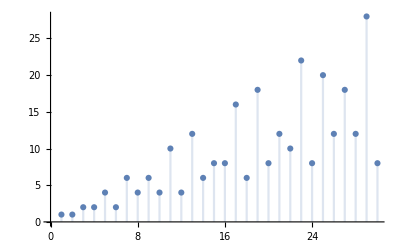

```mathematica
DiscretePlot[EulerPhi[k],{k,30},AxesOrigin->{0,0}]
```

```mathematica
Total[Map[EulerPhi[#]&,Divisors[100]]]
```

100

```mathematica
Divisors[100]
EulerPhi[100]
Total[Map[MoebiusMu[100/#]#&,Divisors[100]]]
```

{1,2,4,5,10,20,25,50,100}

40

40

## Dirichlet Multiplication ( Convolution )

### Definition

The Dirichlet convolution (f *g)(m) of two functions f(n) and g(n) is given by ∑_(d∣m) f(d) g(m/d).

#### Example

```mathematica
DirichletConvolve[MoebiusMu[n],id[n],n,12]
```

0

```mathematica
DirichletConvolve[MoebiusMu[n],u[n],n,12]
```

0

```mathematica
DirichletConvolve[MoebiusMu[n],n,n,12]
```

4

```mathematica
DirichletConvolve[MoebiusMu[n]^2 EulerPhi[n]^-1,u[n],n,12]
```

3

```mathematica
Table[{k,Log[2,DirichletConvolve[MoebiusMu[n]^2,u[n],n,k]],Total[Map[MoebiusMu[#]^2&,Divisors[k]]],2^PrimeNu[k]},{k,1,10}]//tf
```

1 | 0 | 1 | 1
2 | 1 | 2 | 2
3 | 1 | 2 | 2
4 | 1 | 2 | 2
5 | 1 | 2 | 2
6 | 2 | 4 | 4
7 | 1 | 2 | 2
8 | 1 | 2 | 2
9 | 1 | 2 | 2
10 | 2 | 4 | 4

```mathematica
DirichletConvolve[MoebiusMu[n],Log[n],n,729]//Simplify
```

Log[3]

Averages of Arithmetical Functions

## EulerGamma Constant

#### Example

```mathematica
ClearAll[f]
f[x_]:=Sum[1/k,{k,1,x}]-Integrate[1/y,{y,1,x}]
Limit[f[x],x->Infinity]
```

EulerGamma

```mathematica
EulerGamma//N
```

0.577216

```mathematica
f[1]
f[2]//N
```

1

0.806853

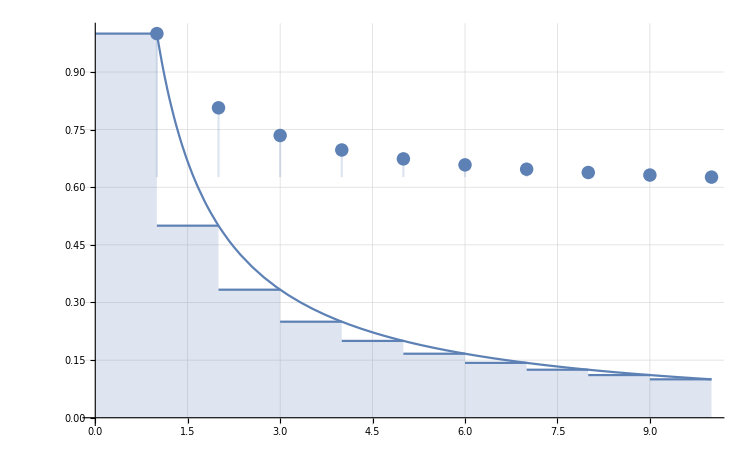

```mathematica
Clear[pl]
pl[x_]:=Show[DiscretePlot[f[k],{k,1,Floor[x]}],DiscretePlot[1/k,{k,1,Floor[x]},ExtentSize->Left],Plot[1/y,{y,.4,x}],GridLines->Automatic,PlotRange->Full,AxesOrigin->{0,0}]
pl[10]
```

## Some Elementary Asymptotic Formulas

### Theorem: ∑_(n≤ x) 1/n = Log(x)+γ +O(1/x)

#### Proof

```mathematica
HoldForm[Integrate[f[t],{t,1,x}]+Integrate[(t-Floor[t])f'[t],{t,1,x}]+f[1]+(Floor[x]-x)f[x]]//TraditionalForm
HoldForm[Integrate[1/t,{t,1,x}]+Integrate[(t-Floor[t])-1/t^2,{t,1,x}]+1+(Floor[x]-x)/x]//TraditionalForm
HoldForm[Log[x]+1-Integrate[(t-Floor[t])1/t^2,{t,1,x}]-(x-Floor[x])/x]//TraditionalForm
HoldForm[Log[x]+1-Integrate[(t-Floor[t])1/t^2,{t,1,x}]+O[1/x]]//TraditionalForm
HoldForm[Log[x]+1-Integrate[(t-Floor[t])1/t^2,{t,1,Infinity}]+Integrate[(t-Floor[t])1/t^2,{t,x,Infinity}]+O[1/x]]//TraditionalForm
HoldForm[Log[x]+(1-Integrate[(t-Floor[t])1/t^2,{t,1,Infinity}])+O[1/x]]//TraditionalForm
HoldForm[Log[x]+EulerGamma+O[1/x]]//TraditionalForm
```

∫_1^x f(t)ⅆt+∫_1^x (t-Floor[t]) f'(t)ⅆt+f(1)+(Floor[x]-x) f(x)

∫_1^x 1/t ⅆt+∫_1^x ((t-Floor[t])-1/t^2)ⅆt+1+(Floor[x]-x)/x

log(x)+1-∫_1^x (t-Floor[t])/t^2 ⅆt-(x-Floor[x])/x

log(x)+1-∫_1^x (t-Floor[t])/t^2 ⅆt+O(1/x)

log(x)+1-∫_1^∞ (t-Floor[t])/t^2 ⅆt+∫_x^∞ (t-Floor[t])/t^2 ⅆt+O(1/x)

log(x)+(1-∫_1^∞ (t-Floor[t])/t^2 ⅆt)+O(1/x)

log(x)+ℽ+O(1/x)

#### Example

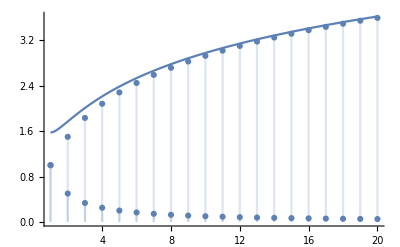

```mathematica
ClearAll[pl]
pl[n_]:=Show[DiscretePlot[1/x,{x,1,n}],DiscretePlot[Sum[1/y,{y,1,x}],{x,1,n}],Plot[Log[x]+EulerGamma+ 1/x,{x ,1,n}],PlotRange->All]
pl[20]
```

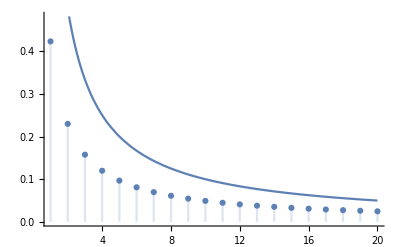

True

```mathematica
pl1[n_]:=Show[DiscretePlot[{Sum[1/y,{y,1,x}]-(Log[x]+EulerGamma )},{x,1,n}],Plot[ 1/x,{x ,1,n}],PlotRange->All,AxesOrigin->{0,0}]
pl1[20]
(Sum[1/y,{y,1,20}]-(Log[20]+EulerGamma))<1/20
```

### Theorem: ∑_(n≤ x) 1/n^s = x^(1-s)/(1-s)+ζ(s) +O(1/x^s)

#### Proof

```mathematica
HoldForm[Integrate[f[t],{t,1,x}]+Integrate[(t-Floor[t])f'[t],{t,1,x}]+f[1]+(Floor[x]-x)f[x]]//TraditionalForm
HoldForm[Integrate[1/t^s,{t,1,x}]-s Integrate[(t-Floor[t])/t^(s+1),{t,1,x}]+1-(x-Floor[x])/x]//TraditionalForm
HoldForm[Integrate[1/t^s,{t,1,x}]+1-s Integrate[(t-Floor[t])/t^(s+1),{t,1,x}]+O[1/x^s]]//TraditionalForm
HoldForm[x^(1-s)/(1-s)-1/(1-s)+1-s Integrate[(t-Floor[t])/t^(s+1),{t,1,x}]+O[1/x^s]]//TraditionalForm
HoldForm[x^(1-s)/(1-s)+(1-1/(1-s)-s Integrate[(t-Floor[t])/t^(s+1),{t,1,x}])+O[1/x^s]]//TraditionalForm
HoldForm[x^(1-s)/(1-s)+Zeta[s]+O[1/x^s]]//TraditionalForm
```

∫_1^x f(t)ⅆt+∫_1^x (t-Floor[t]) f'(t)ⅆt+f(1)+(Floor[x]-x) f(x)

∫_1^x 1/t^s ⅆt-s ∫_1^x (t-Floor[t])/t^(s+1)ⅆt+1-(x-Floor[x])/x

∫_1^x 1/t^s ⅆt+1-s ∫_1^x (t-Floor[t])/t^(s+1)ⅆt+O(1/x^s)

x^(1-s)/(1-s)-1/(1-s)+1-s ∫_1^x (t-Floor[t])/t^(s+1)ⅆt+O(1/x^s)

x^(1-s)/(1-s)+(1-1/(1-s)-s ∫_1^x (t-Floor[t])/t^(s+1)ⅆt)+O(1/x^s)

x^(1-s)/(1-s)+s+O(1/x^s)

#### Example

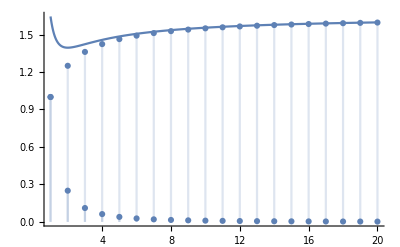

```mathematica
ClearAll[pl]
pl[n_,s_]:=Show[DiscretePlot[1/x^s,{x,1,n}],DiscretePlot[Sum[1/y^s,{y,1,x}],{x,1,n}],Plot[x^(1-s)/(1-s)+Zeta[s]+ 1/x^s,{x ,1,n}],PlotRange->All]
pl[20,2]
```

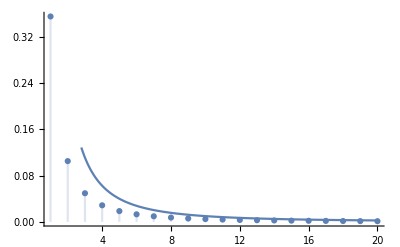

True

```mathematica
pl1[n_,s_]:=Show[DiscretePlot[{Sum[1/y^s,{y,1,x}]-(x^(1-s)/(1-s)+Zeta[s])},{x,1,n}],Plot[ 1/x^s,{x ,1,n}],PlotRange->All,AxesOrigin->{0,0}]
pl1[20,2]
(Sum[1/y^2,{y,1,20}]-(20^-1/-1+Zeta[2]))<1/10^2
```

### Theorem: ∑_(n>x) 1/n^s = O(x^(1-s))

#### Proof

```mathematica
HoldForm[Zeta[s]-(x^(1-s)/(1-s)+Zeta[s]+O[1/x^s])]//TraditionalForm
HoldForm[x^(1-s)/(s-1)+O[1/x^s]]//TraditionalForm
HoldForm[O[x^(1-s)]]//TraditionalForm
```

s-(x^(1-s)/(1-s)+s+O(1/x^s))

x^(1-s)/(s-1)+O(1/x^s)

O(x^(1-s))

### Theorem: ∑_(n≤ x) n^α =x^(α+1)/(α+1)+O(x^α )

#### Proof

```mathematica
HoldForm[Integrate[f[t],{t,1,x}]+Integrate[(t-Floor[t])f'[t],{t,1,x}]+f[1]+(Floor[x]-x)f[x]]//TraditionalForm
HoldForm[Integrate[t^α,{t,1,x}]+Integrate[(t-Floor[t])α t^(α-1),{t,1,x}]+1+(Floor[x]-x)x^α]//TraditionalForm
HoldForm[x^(α+1)/(α+1)-1/(α+1)+Integrate[(t-Floor[t])α t^(α-1),{t,1,x}]+1+(Floor[x]-x)x^α]//TraditionalForm
HoldForm[x^(α+1)/(α+1)-1/(α+1)+O[α Integrate[ t^(α-1),{t,1,x}]]+1+O[x^α]]//TraditionalForm
HoldForm[x^(α+1)/(α+1)-1/(α+1)+O[-1+x^α]+1+O[x^α]]//TraditionalForm
HoldForm[x^(α+1)/(α+1)+O[x^α]]//TraditionalForm
```

∫_1^x f(t)ⅆt+∫_1^x (t-Floor[t]) f'(t)ⅆt+f(1)+(Floor[x]-x) f(x)

∫_1^x t^α ⅆt+∫_1^x (t-Floor[t]) α t^(α-1)ⅆt+1+(Floor[x]-x) x^α

x^(α+1)/(α+1)-1/(α+1)+∫_1^x (t-Floor[t]) α t^(α-1)ⅆt+1+(Floor[x]-x) x^α

x^(α+1)/(α+1)-1/(α+1)+O(α ∫_1^x t^(α-1)ⅆt)+1+O(x^α)

x^(α+1)/(α+1)-1/(α+1)+O(-1+x^α)+1+O(x^α)

x^(α+1)/(α+1)+O(x^α)

#### Example

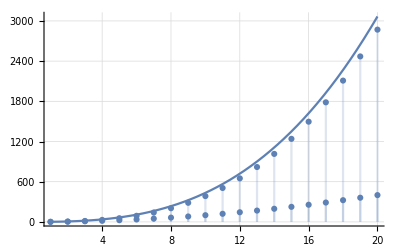

```mathematica
ClearAll[pl]
pl[n_,a_]:=Show[DiscretePlot[x^a,{x,1,n}],DiscretePlot[Sum[y^a,{y,1,x}],{x,1,n}],Plot[x^(a+1)/(a+1)+x^a,{x ,1,n}],PlotRange->All,GridLines->Automatic]
pl[20,2]
```

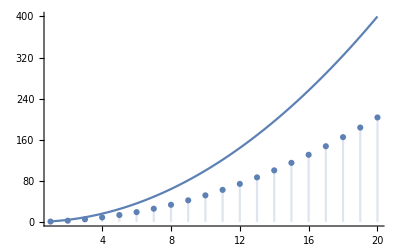

True

```mathematica
pl1[n_,a_]:=Show[DiscretePlot[{Sum[y^a,{y,1,x}]-x^(a+1)/(a+1)},{x,1,n}],Plot[ x^a ,{x ,1,n}],PlotRange->All,AxesOrigin->{0,0}]
pl1[20,2]
(Sum[1/y,{y,1,20}]-20^3/3)<20^2
```

## Asymptotic Formulas for Arithmetical Functions

### Theorem: ∑_(n≤ x) τ(n) = x Log(x)+(2γ-1)x +O(√x)

#### Introduction

Formulas for calculating ∑_(n≤ x) τ(n)

```mathematica
ClearAll[nDiv1,nDiv2,nDiv3,nDiv4];
nDiv1[z_]:=Sum[DivisorSigma[0,y],{y,1,Floor[z]}]
nDiv2[z_]:=Total[Map[Length[Solve[y==#/x&&x>0&&y>0,{x,y},Integers]]&,Range[Floor[z]]]]
nDiv3[z_]:=Total[Map[Floor[z/#]&,Range[Floor[z]]]]
nDiv4[z_]:=2Sum[Floor[z/k]-k,{k,1,Floor[Sqrt[z]]}]+Floor[√z]
{nDiv1[10],nDiv2[10],nDiv3[10],nDiv4[10]}
```

{27,27,27,27}

#### Proof

```mathematica
HoldForm[2Sum[Floor[x/k]-k,{k,1,Floor[Sqrt[x]]}]+Floor[√x]]//TraditionalForm
HoldForm[2Sum[x/k-k+O[1],{k,1,Floor[Sqrt[x]]}]+O[√x]]//TraditionalForm
HoldForm[2Sum[x/k,{k,1,Floor[Sqrt[x]]}]-2Sum[k,{k,1,Floor[Sqrt[x]]}]+O[√x]]//TraditionalForm
HoldForm[2x Sum[1/k,{k,1,Floor[Sqrt[x]]}]-2Sum[k,{k,1,Floor[Sqrt[x]]}]+O[√x]]//TraditionalForm
HoldForm[2x  (Log[√x]+γ +O[1/(√x)])-2Sum[k,{k,1,Floor[Sqrt[x]]}]+O[√x]]//TraditionalForm
HoldForm[x  Log[x]+2γ  x -2Sum[k,{k,1,Floor[Sqrt[x]]}]+O[√x]]//TraditionalForm
HoldForm[x  Log[x]+2γ  x -2(x/2+O[√x])+O[√x]]//TraditionalForm
HoldForm[x  Log[x]+(2γ -1) x +O[√x]]//TraditionalForm
```

2 ∑_(k=1)^Floor[√x] (Floor[x/k]-k)+Floor[√x]

2 ∑_(k=1)^Floor[√x] (x/k-k+O(1))+O(√x)

2 ∑_(k=1)^Floor[√x] x/k-2 ∑_(k=1)^Floor[√x] k+O(√x)

2 x ∑_(k=1)^Floor[√x] 1/k-2 ∑_(k=1)^Floor[√x] k+O(√x)

2 x (log(√x)+γ+O(1/(√x)))-2 ∑_(k=1)^Floor[√x] k+O(√x)

x log(x)+2 γ x-2 ∑_(k=1)^Floor[√x] k+O(√x)

x log(x)+2 γ x-2 (x/2+O(√x))+O(√x)

x log(x)+(2 γ-1) x+O(√x)

#### Example

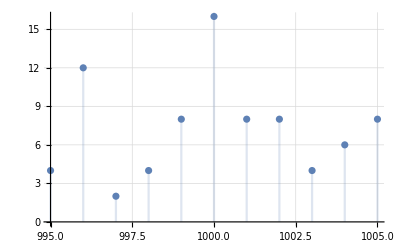

```mathematica
ClearAll[pl0]
pl0[n_,m_]:=Show[DiscretePlot[DivisorSigma[0,x],{x,n,m}],GridLines->Automatic,PlotRange->All]
pl0[995,1005]
```

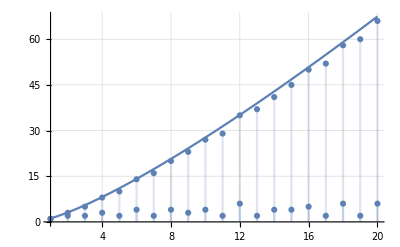

```mathematica
ClearAll[pl]
pl[n_]:=Show[
DiscretePlot[DivisorSigma[0,x],{x,1,n}],
DiscretePlot[Sum[DivisorSigma[0,y],{y,1,x}],{x,1,n}],
Plot[x Log[x]+x(2 EulerGamma -1 )+ √x,{x ,1,n}],
GridLines->Automatic,PlotRange->All]
pl[20]
```

True

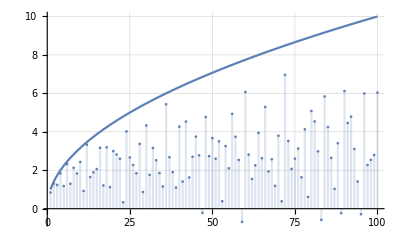

```mathematica
pl1[n_]:=Show[DiscretePlot[{Sum[DivisorSigma[0,y],{y,1,x}]-(x Log[x]+(2 EulerGamma -1 )x)},{x,1,n}],Plot[ √x,{x ,1,n}],PlotRange->All,GridLines->Automatic,AxesOrigin->{0,0}]
Sum[DivisorSigma[0,y],{y,1,100}]-(100Log[100]+(2EulerGamma-1)100)<√100
pl1[100]
```

### Theorem: ∑_(n≤ x) σ(n) = 1/2 ζ(2)x^2+O(x Log(x))

#### Introduction

Formulas for calculating ∑_(n≤ x) σ(n)

```mathematica
ClearAll[nDiv1,nDiv2,nDiv3,nDiv4];
nDiv1[z_]:=Sum[DivisorSigma[1,y],{y,1,Floor[z]}]
nDiv2[z_]:=Total[Map[#[[1,2]]&,Flatten[Map[Map[#&,Solve[y==#/x&&x>0&&y>0,{x,y},Integers]]&,Range[Floor[z]]],1]]]
nDiv3[z_]:=Total[Map[# Floor[z/#]&,Range[Floor[z]]]]
nDiv4[z_]:=Sum[Sum[q,{q,1,Floor[z/d]}],{d,1,Floor[z]}]
{nDiv1[6],nDiv2[6],nDiv3[6],nDiv4[6]}
```

{33,33,33,33}

#### Proof

```mathematica
HoldForm[Sum[Sum[q,{q,1,Floor[x/d]}],{d,1,Floor[x]}]]//TraditionalForm
HoldForm[Sum[1/2(x/d)^2+O[x/d],{d,1,Floor[x]}]]//TraditionalForm
HoldForm[1/2 x^2 Sum[1/d^2,{d,1,Floor[x]}]+O[x Sum[1/d,{d,1,Floor[x]}]]]//TraditionalForm
HoldForm[1/2 x^2(-1/x+Zeta[2]+O[1/x^2])+O[x Sum[1/d,{d,1,Floor[x]}]]]//TraditionalForm
HoldForm[1/2 x^2(-1/x+Zeta[2]+O[1/x^2])+O[x Log[x]]]//TraditionalForm
HoldForm[1/2 Zeta[2] x^2+O[x Log[x]]]//TraditionalForm
```

∑_(d=1)^Floor[x] (∑_(q=1)^Floor[x/d] q)

∑_(d=1)^Floor[x] (1/2 (x/d)^2+O(x/d))

1/2 x^2 ∑_(d=1)^Floor[x] 1/d^2+O(x ∑_(d=1)^Floor[x] 1/d)

1/2 x^2 (-1/x+2+O(1/x^2))+O(x ∑_(d=1)^Floor[x] 1/d)

1/2 x^2 (-1/x+2+O(1/x^2))+O(x log(x))

(2 x^2)/2+O(x log(x))

#### Example

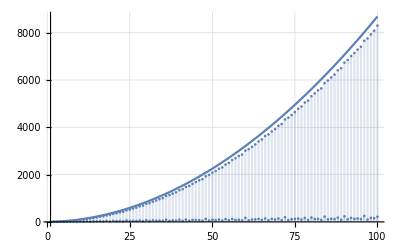

```mathematica
ClearAll[pl]
pl[n_]:=Show[DiscretePlot[DivisorSigma[1,x],{x,1,n}],DiscretePlot[Sum[DivisorSigma[1,y],{y,1,x}],{x,1,n}],Plot[1/2 Zeta[2] x^2+x Log[x],{x ,1,n}],
GridLines->Automatic,PlotRange->All]
pl[100]
```

True

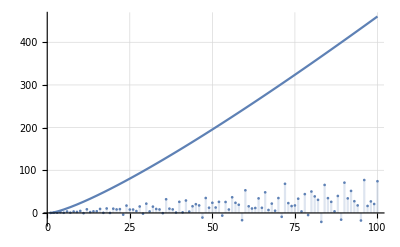

```mathematica
pl1[n_]:=Show[DiscretePlot[{Sum[DivisorSigma[1,y],{y,1,x}]-1/2 Zeta[2] x^2},{x,1,n}],Plot[ x Log[x],{x ,1,n}],PlotRange->All,GridLines->Automatic,AxesOrigin->{0,0}]
Sum[DivisorSigma[1,y],{y,1,100}]-(1/2 100^2 Zeta[2])<100Log[100]
pl1[100]
```

### Theorem: ∑_(n≤ x) σ_α(n) = 1/(α+1)ζ(α+1)x^2+O(x^Max[1,α])

#### Introduction

Formulas for calculating ∑_(n≤ x) σ_α(n)

```mathematica
ClearAll[nDiv1,nDiv4];
nDiv1[z_,a_]:=Sum[DivisorSigma[a,y],{y,1,Floor[z]}]
nDiv4[z_,a_]:=Sum[Sum[q^a,{q,1,Floor[z/d]}],{d,1,Floor[z]}]
{nDiv1[6,2],nDiv4[6,2]}
```

{113,113}

#### Proof

```mathematica
HoldForm[Sum[Sum[q^α,{q,1,Floor[x/d]}],{d,1,Floor[x]}]]//TraditionalForm
HoldForm[Sum[1/(α+1)(x/d)^(α+1)+O[x^α/d^α],{d,1,Floor[x]}]]//TraditionalForm
HoldForm[1/(α+1) x^(α+1) Sum[1/d^(α+1),{d,1,Floor[x]}]+O[x^α Sum[1/d^α,{d,1,Floor[x]}]]]//TraditionalForm
HoldForm[1/(α+1) x^(α+1)(x^-α/-α+Zeta[α+1]+O[x^(-α-1)])+O[x^α (x^(1-α)/(1-α)+Zeta[α]+O[x^-α])]]//TraditionalForm
HoldForm[1/(α+1) Zeta[α+1] x^(α+1)+O[x]+O[1]+O[x^α]]//TraditionalForm
HoldForm[1/(α+1) Zeta[α+1] x^(α+1)+O[x^Max[1,α]]]//TraditionalForm
```

∑_(d=1)^Floor[x] (∑_(q=1)^Floor[x/d] q^α)

∑_(d=1)^Floor[x] ((x/d)^(α+1)/(α+1)+O(x^α/d^α))

(x^(α+1) ∑_(d=1)^Floor[x] 1/d^(α+1))/(α+1)+O(x^α ∑_(d=1)^Floor[x] 1/d^α)

(x^(α+1) (-x^-α/α+α+1+O(x^(-α-1))))/(α+1)+O(x^α (x^(1-α)/(1-α)+α+O(x^-α)))

(α+1 x^(α+1))/(α+1)+O(x)+O(1)+O(x^α)

(α+1 x^(α+1))/(α+1)+O(x^(max(1,α)))

#### Example

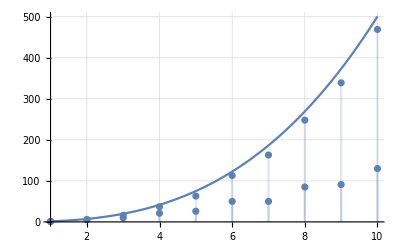

```mathematica
ClearAll[pl]
pl[n_,a_]:=Show[DiscretePlot[DivisorSigma[a,x],{x,1,n}],DiscretePlot[Sum[DivisorSigma[a,y],{y,1,x}],{x,1,n}],Plot[1/(a+1)Zeta[a+1] x^(a+1)+x^Max[1,a],{x ,1,n}],
GridLines->Automatic,PlotRange->All]
pl[10,2]
```

### Theorem: ∑_(n≤ x) σ_-β(n) = ζ(β+1)x+O(x^Max[0,1-β]) if β≠1

#### Introduction

Formulas for calculating ∑_(n≤ x) σ_-β(n)

```mathematica
ClearAll[nDiv1,nDiv4];
nDiv1[z_,b_]:=Sum[DivisorSigma[-b,y],{y,1,Floor[z]}] 
nDiv4[z_,b_]:=Sum[Sum[q^-b,{q,1,Floor[z/d]}],{d,1,Floor[z]}]
nDiv4A[z_,b_]:=Sum[1/d^b Sum[1,{q,1,Floor[z/d]}],{d,1,Floor[z]}]
{nDiv1[6,2],nDiv4[6,2],nDiv4A[6,2]}
```

{2841/400,2841/400,2841/400}

#### Proof

```mathematica
HoldForm[Sum[1/d^b Sum[1,{q,1,Floor[x/d]}],{d,1,Floor[x]}]]//TraditionalForm
HoldForm[Sum[1/d^b(x/d+O[1]),{d,1,Floor[x]}]]//TraditionalForm
HoldForm[x Sum[1/d^(b+1),{d,1,Floor[x]}]+O[Sum[1/d^b,{d,1,Floor[x]}]]]//TraditionalForm
HoldForm[x^(1-b)/-b Zeta[b+1]x+O[x^-b]]//TraditionalForm
HoldForm[ Zeta[b+1]x+O[x^Max[0,1-b]]]//TraditionalForm
```

∑_(d=1)^Floor[x] (∑_(q=1)^Floor[x/d] 1)/d^b

∑_(d=1)^Floor[x] (x/d+O(1))/d^b

x ∑_(d=1)^Floor[x] 1/d^(b+1)+O(∑_(d=1)^Floor[x] 1/d^b)

-(x^(1-b) b+1 x)/b+O(x^-b)

b+1 x+O(x^(max(0,1-b)))

#### Example

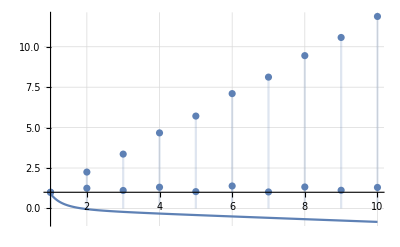

```mathematica
ClearAll[pl]
pl[n_,b_]:=Show[
DiscretePlot[DivisorSigma[b,x],{x,1,n}],
DiscretePlot[Sum[DivisorSigma[b,y],{y,1,x}],{x,1,n}],
Plot[Zeta[b+1]x+1/x^(1-b),{x ,1,n}],
GridLines->Automatic,PlotRange->All]
pl[10,-2]
```

### Theorem: ∑_(n≤ x) ϕ(n) = 3/π^2 x^2+O(x Log[x])

#### Introduction

Formulas for calculating ∑_(n≤ x) ϕ(n)

```mathematica
ClearAll[nPhi1,nPhi2];
nPhi1[z_]:=Sum[EulerPhi[y],{y,1,Floor[z]}]
nPhi2[z_]:=Sum[MoebiusMu[d]Sum[q,{q,1,Floor[z/d]}],{d,1,Floor[z]}]
{nPhi1[50],nPhi2[50]}
```

{774,774}

#### Proof

```mathematica
HoldForm[Sum[MoebiusMu[d]Sum[q,{q,1,Floor[x/d]}],{d,1,Floor[x]}]]//TraditionalForm
HoldForm[ Sum[MoebiusMu[d](1/2(x/d)^2+O[x/d]),{d,1,Floor[x]}]]//TraditionalForm
HoldForm[1/2 x^2 Sum[MoebiusMu[d]/d^2,{d,1,Floor[x]}]+O[x Sum[1/d,{d,1,Floor[x]}]]]//TraditionalForm
HoldForm[1/2 x^2 6/π^2+O[x Sum[1/d,{d,1,Floor[x]}]]]//TraditionalForm
HoldForm[3/π^2 x^2+O[x Log[x]]]//TraditionalForm
```

∑_(d=1)^Floor[x] d ∑_(q=1)^Floor[x/d] q

∑_(d=1)^Floor[x] d (1/2 (x/d)^2+O(x/d))

1/2 x^2 ∑_(d=1)^Floor[x] d/d^2+O(x ∑_(d=1)^Floor[x] 1/d)

(x^2 6)/(2 π^2)+O(x ∑_(d=1)^Floor[x] 1/d)

(3 x^2)/π^2+O(x log(x))

#### Example

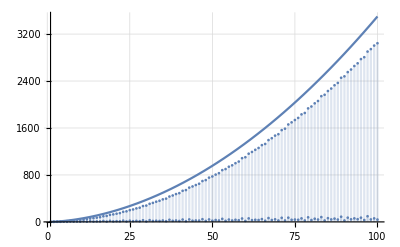

```mathematica
ClearAll[pl]
pl[n_]:=Show[DiscretePlot[EulerPhi[x],{x,1,n}],DiscretePlot[Sum[EulerPhi[y],{y,1,x}],{x,1,n}],Plot[3/π^2 x^2+x Log[x],{x ,1,n}],
GridLines->Automatic,PlotRange->All]
pl[100]
```

True

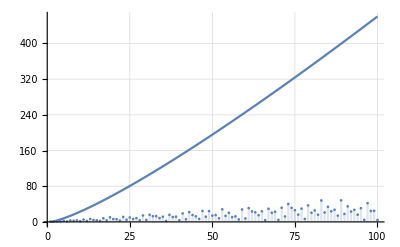

```mathematica
pl1[n_]:=Show[DiscretePlot[{
Sum[EulerPhi[y],{y,1,x}]-3/π^2 x^2},{x,1,n}],Plot[ x Log[x],{x ,1,n}],PlotRange->All,GridLines->Automatic,AxesOrigin->{0,0}]
Sum[EulerPhi[y],{y,1,100}]-(3/π^2 100^2)<100Log[100]
pl1[100]
```

## An application to the distribution of lattice points visible from the origin

### Theorem: Apo 3.8

### Theorem: Apo 3.9

## Partial Sums of a Dirichlet Product

### Theorem: Apo 3.10

### Theorem: Apo 3.11

### Theorem: Apo 3.12

### Theorem: Apo 3.13

### Theorem: Apo 3.14

### Theorem: Apo 3.15

### Theorem: Apo 3.16

### Theorem: Apo 3.17

## Exercises

### Apo 3.1 a)

### Apo 3.1 b)

### Apo 3.2)

### Apo 3.3)

Distribution of Prime Numbers

## Suppose π(n)=A ; for which m is π(m)=2A

```mathematica
Reduce[x/Log[x]==(2 y)/Log[y],x,Integers]
```

(x|y)∈ℤ&&((ProductLog[-Log[y]/(2 y)]≠0&&y≥2&&x==ⅇ^(-ProductLog[-Log[y]/(2 y)]))||(ProductLog[-1,-Log[y]/(2 y)]≠0&&y≥2&&x==ⅇ^(-ProductLog[-1,-Log[y]/(2 y)])))

```mathematica
ClearAll[f,g]
f[y_]:=ⅇ^(-ProductLog[-1,-Log[y]/(2 y)])
g[x_]:=x/Log[x]
```

```mathematica
f[100.]
2g[100.]
g[237.]
```

237.581

43.4294

43.3426

## Sieve of Erasthostenes

```mathematica
ClearAll[f]
f[n_]:=ArrayPlot[Partition[Table[PrimeQ[k]/.{False->0,True->1},{k,n+1,n+10000}],100]]
```

```mathematica
f[1000000]
```

-Graphics-

```mathematica
Table[PrimePi[10^k],{k,1,9}]
```

{4,25,168,1229,9592,78498,664579,5761455,50847534}

## ChebyshevPsi and ChebyshevTheta

### Definition Psi, Theta

ψ(x) = ∑_n Λ(n)
θ(x) = ∑_p Log(p)

```mathematica
chebyshevPsi[x_]:=Sum[MangoldtLambda[y],{y,x}]
chebyshevTheta[x_]:=Sum[Log[k],{k,Select[Range[x],PrimeQ]}]
chebyshevPsi1[x_]:=Sum[chebyshevTheta[x^(1/m)],{m,1,Log[2,x]}]
```

#### Example

```mathematica
chebyshevPsi[10]
chebyshevTheta[10]+chebyshevTheta[3]+chebyshevTheta[2]
```

3 Log[2]+2 Log[3]+Log[5]+Log[7]

3 Log[2]+2 Log[3]+Log[5]+Log[7]

```mathematica
Table[{x,chebyshevPsi[x],chebyshevPsi1[x]},{x,10}]//tf
```

1 | 0 | 0
2 | Log[2] | Log[2]
3 | Log[2]+Log[3] | Log[2]+Log[3]
4 | 2 Log[2]+Log[3] | 2 Log[2]+Log[3]
5 | 2 Log[2]+Log[3]+Log[5] | 2 Log[2]+Log[3]+Log[5]
6 | 2 Log[2]+Log[3]+Log[5] | 2 Log[2]+Log[3]+Log[5]
7 | 2 Log[2]+Log[3]+Log[5]+Log[7] | 2 Log[2]+Log[3]+Log[5]+Log[7]
8 | 3 Log[2]+Log[3]+Log[5]+Log[7] | 3 Log[2]+Log[3]+Log[5]+Log[7]
9 | 3 Log[2]+2 Log[3]+Log[5]+Log[7] | 3 Log[2]+2 Log[3]+Log[5]+Log[7]
10 | 3 Log[2]+2 Log[3]+Log[5]+Log[7] | 3 Log[2]+2 Log[3]+Log[5]+Log[7]

### Theorem:

0 ⩽(ψ(x))/x-(ϑ(x))/x⩽(Log(x))^2/(2 √x Log(2))

#### Example

```mathematica
Table[{x,chebyshevPsi[x]/x-chebyshevTheta[x]/x//N,Log[x]^2/(2 √x Log[2.])},{x,500000,1500000,500000}]//tf
```

500000 | 0.00159035 | 0.175664
1000000 | 0.00110242 | 0.137682
1500000 | 0.000902378 | 0.119113

#### Proof:

```mathematica
ClearAll[t1,t2,T1,T2];
t1[x_]:=chebyshevPsi[x]-chebyshevTheta[x]
t2[x_]:=Sum[chebyshevTheta[x^(1/m)],{m,2,Log[2,x]}]
T1[x_]:=Log[2,x] √x Log[√x]
T2[x_]:=Log[x]^2/(2 √x Log[2.])
```

```mathematica
t2[1000]//N
T1[1000]/1000//N
T2[1000]//N
```

40.4356

1.08847

1.08847

```mathematica
chebyshevTheta[100000]//N
100000Log[100000.]
```

99685.4

1.15129×10^6

### Theorem:

θ(x) =π(x) Log(x)-∫_2^x (π(t))/t ⅆt

#### Proof:

Let a(n) be the characteristic function of the primes.
Then ∑_(1<n≤x) a(n)=π(x) , i.e. the prime-counting function.
Then θ(x) = ∑_(p≤x) Log(p) = ∑_(1<n≤x) a(n)Log(n) .
Finally, by applying Abel Summation:
θ(x) =π(x) Log(x)-∫_2^x (π(t))/t ⅆt.

### Theorem:

π(x) =(θ(x))/(Log(x))+∫_2^x (θ(t))/(t (Log(t))^2)ⅆt

#### Proof:

TBD:

Finally, by applying Abel Summation:
π(x) =(θ(x))/(Log(x))+∫_2^x (θ(t))/(t (Log(t))^2)ⅆt.

## Equivalent forms of the PNT

## Inequalities for π(n) and p_n

## Shapiro’s Tauberian Theorem

## Exercises

### Apo 4.1

### Apo 4.2

```mathematica
Map[PrimeQ[#]||#==1&,Table[Mod[Prime[x],6],{x,169,279}]]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
PrimeQ[113]
```

True

```mathematica
Prime[172]
```

1021

```mathematica
FactorInteger[187]
```

{{11,1},{17,1}}

### Apo 4.3

```mathematica
Table[{x,x^2+x+41,PrimeQ[x^2+x+41]},{x,0,40}]//tf
```

0 | 41 | True
1 | 43 | True
2 | 47 | True
3 | 53 | True
4 | 61 | True
5 | 71 | True
6 | 83 | True
7 | 97 | True
8 | 113 | True
9 | 131 | True
10 | 151 | True
11 | 173 | True
12 | 197 | True
13 | 223 | True
14 | 251 | True
15 | 281 | True
16 | 313 | True
17 | 347 | True
18 | 383 | True
19 | 421 | True
20 | 461 | True
21 | 503 | True
22 | 547 | True
23 | 593 | True
24 | 641 | True
25 | 691 | True
26 | 743 | True
27 | 797 | True
28 | 853 | True
29 | 911 | True
30 | 971 | True
31 | 1033 | True
32 | 1097 | True
33 | 1163 | True
34 | 1231 | True
35 | 1301 | True
36 | 1373 | True
37 | 1447 | True
38 | 1523 | True
39 | 1601 | True
40 | 1681 | False

```mathematica
Table[Prime[x],{x,26,46}]//tf
```

101
103
107
109
113
127
131
137
139
149
151
157
163
167
173
179
181
191
193
197
199

tmp’s

## tmp-1: Alternate Prime Definitions; No more Unique Prime Factorization

```mathematica
Divisors[46 51]
```

{1,2,3,6,17,23,34,46,51,69,102,138,391,782,1173,2346}

```mathematica
Divisors[391]
```

{1,17,23,391}

```mathematica
46 51
```

2346

```mathematica
6 391
```

2346

```mathematica
Divisors[391]
```

{1,17,23,391}

```mathematica
Divisors[21 46]
```

{1,2,3,6,7,14,21,23,42,46,69,138,161,322,483,966}

```mathematica
6 161
```

966

```mathematica
Divisors[161]
```

{1,7,23,161}

```mathematica
ClearAll[g]
g[x_]:=10^x
```

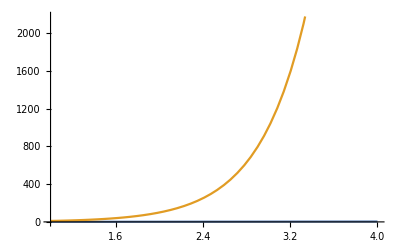

0.30103

0.30103

```mathematica
Plot[{x,g[x]},{x,1,4}]
Log[10,200.]-Log[10,100.]
Log[10,400.]-Log[10,200.]
```

## tmp-2

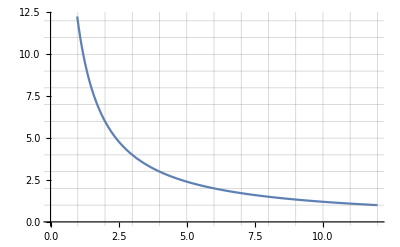

```mathematica
Plot[12/x,{x,0,12},AxesOrigin->{0,0}, GridLines->All]
```

```mathematica
8500000*.02
```

170000.

```mathematica
HarmonicNumber[4]
```

25/12

```mathematica
EulerPhi[40]
```

16

```mathematica
ClearAll[f,n];
f[t_]:=t^2+t
Integrate[f'[t],{t,n-1,n}]//Expand
f[n]-f[n-1]//Expand
```

2 n

2 n

```mathematica
D[1/t,{t,1}]
```

-1/t^2

```mathematica
ClearAll[f,g,s,t];
f[n_]:=106 1.4^(n-1)
g[n_]:=106  (1+(40/100-n))^(n-1)
s[n_]:=106 (1-1.4^n)/(1-1.4)
Table[{n,f[n],s[n]},{n,1,7}]//tf
```

1 | 106. | 106.
2 | 148.4 | 254.4
3 | 207.76 | 462.16
4 | 290.864 | 753.024
5 | 407.21 | 1160.23
6 | 570.093 | 1730.33
7 | 798.131 | 2528.46

```mathematica
Log[10]/Log[2]//N
ⅇ^Log[2]
```

3.32193

2

## tmp-3